# Cosmology PSET 6:

```mathematica
vMap=ResourceFunction["ViridisColor"];
```

```mathematica
params={Ωd ->5/6,Ωb->1/6};
```

```mathematica
odeD = D[f[t],{t,2}]+4/(3 t)D[f[t],t] -2/(3 t^2)(Ωd f[t]+Ωb g[t])==0
```

-(2 (Ωd f[t]+Ωb g[t]))/(3 t^2)+(4 f'[t])/(3 t)+f''[t]==0

```mathematica
odeB = D[g[t],{t,2}]+4/(3 t)D[g[t],t] -2/(3 t^2)(Ωd f[t]+Ωb g[t])==0
```

-(2 (Ωd f[t]+Ωb g[t]))/(3 t^2)+(4 g'[t])/(3 t)+g''[t]==0

```mathematica
sysSolution = NDSolveValue[{odeD,odeB, f[1]==1*^-3, g[1]==1*^-4, f'[1]==0, g'[1]==0}/.params, {f,g},{t,1,500}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

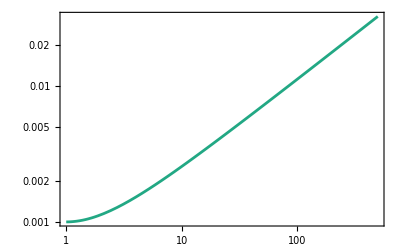

```mathematica
δDPlot = Plot[sysSolution[[1]][t],{t,1,500}, Frame->True, ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.6]]
```

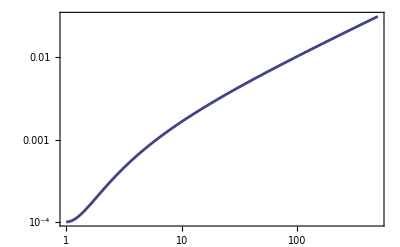

```mathematica
δBPlot =Plot[sysSolution[[2]][t],{t,1,500}, Frame->True, ScalingFunctions->{"Log","Log"}, PlotStyle->vMap[0.2]]
```

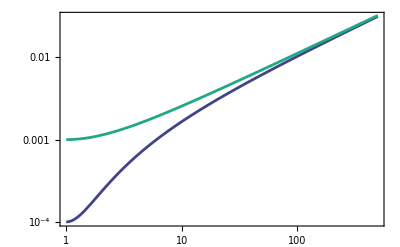

```mathematica
Show[δBPlot ,δDPlot]
```

```mathematica
ratio = (sysSolution[[1]][t])/(sysSolution[[2]][t]);
```

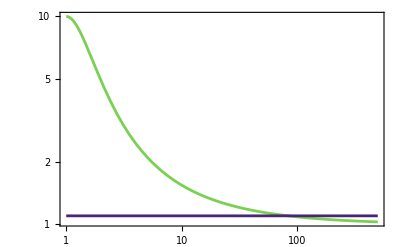

```mathematica
ratioPlot = Plot[{ratio, 1.1},{t,1,500},Frame->True, ScalingFunctions->{"Log","Log"}, PlotStyle->{vMap[0.8],vMap[0.1]} , PlotRange->All]
```

```mathematica
tPerturbation = (t/.FindRoot[ratio==1.1, {t,1,500}]) × 380000
```

3.17432×10^7